# Experiment-7 Joule-Thomson effect

## EP20B012-Chaganti Kamaraja Siddhartha

## Joule Thomson Coefficient of CO_2

```mathematica
p1 =Range[0,0.85,0.05];
t1 ={-0.12,-0.06,-0.02,0.03,0.09,0.14,0.2,0.23,0.31,0.36,0.4,0.46,0.52,0.56,0.6,0.65,0.71,0.75};
```

```mathematica
data1= Transpose[{p1,t1}];
lm1 = LinearModelFit[data1,x,x]
```

FittedModel[-0.116433+1.03344 x]

```mathematica
Normal[lm1]
```

-0.116433+1.03344 x

```mathematica
RootMeanSquare[data1[[All,2]]-#/@data1[[All,1]]]&/@{lm1}
```

{0.00868246}

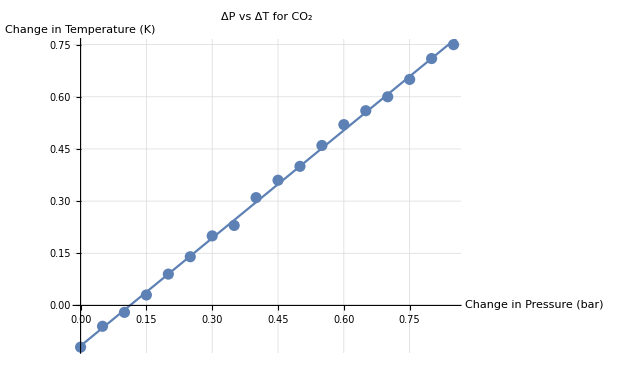

```mathematica
Show[ListPlot[data1, AxesLabel->{"Change in Pressure (bar)", "Change in Temperature (K) "}],Plot[lm1[x],{x,0,1}], PlotLabel->"ΔP vs ΔT for CO_2", GridLines->Automatic]
```

μ_CO_2=(1.03344  ± 0.00868246) x 10^-5  K/pa

## Joule Thomson Coefficient of N_2

```mathematica
p2 = Range[0,1,0.05];
t2 = {-0.08,-0.06,-0.05,-0.04,-0.03,-0.01,-0.01,0.0,0.01,0.01,0.02,0.03,0.04,0.06,0.07,0.08,0.1,0.11,0.11,0.12,0.12};
```

```mathematica
data2 = Transpose[{p2,t2}];
lm2 = LinearModelFit[data2,x,x]
```

FittedModel[-0.0722078+0.201558 x]

```mathematica
Normal[lm2]
```

-0.0722078+0.201558 x

```mathematica
RootMeanSquare[data2[[All,2]]-#/@data2[[All,1]]]&/@{lm2}
```

{0.00637132}

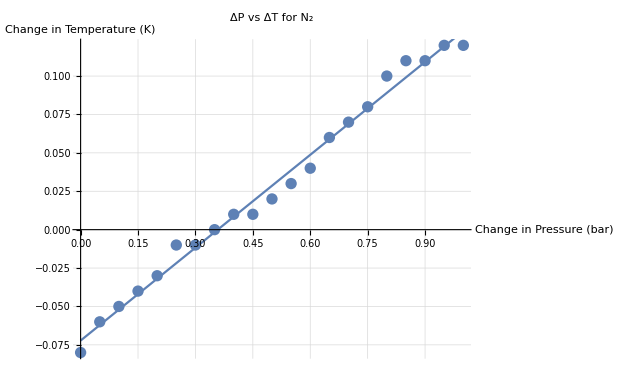

```mathematica
Show[ListPlot[data2, AxesLabel->{"Change in Pressure (bar)", "Change in Temperature (K) "}],Plot[lm2[x],{x,0,1}], PlotLabel->"ΔP vs ΔT for N_2", GridLines->Automatic]
```

μ_N_2=(0.0201588 ± 0.00637132 ) x 10^-5  K/pa